◼ "\◼ "2023-08-14T13:45v1 .00M. J. SteilTU Darmstadt

# Geodesics_HTO1metric

Martin Jakob Steil

Abstract

Initialization

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
$DistributedContexts={};

(* Disable Notebookhistory, [https://mathematica.stackexchange.com/questions/11258/are-there-suitable-versioning-systems-for-mathematica-notebooks]*)
SetOptions[EvaluationNotebook[],PrivateNotebookOptions->{"FileOutlineCache"->False},System`TrackCellChangeTimes->False]

(* Display the Timing of an Evaluation in a Notebook Window [https://reference.wolfram.com/language/howto/DisplayTheTimingOfAnEvaluationInANotebookWindow.html] *)
SetOptions[EvaluationNotebook[],EvaluationCompletionAction->{"ShowTiming"}]

Get["D:/Github/Mathematica/Packages/GeneralRelativity/GR.m"]

c0=299792458;
G=6.67408*10^-11; 
qe=1.6021766208*10^-19;
hbar=1.054571817*10^-34;

hbarcMeVfm=hbar*c0/qe/(10^6*10^-15);

cMeVkm=G*qe/c0^4*10^3;
cfm3km3=1.*10^(18*3);
cMeVfm3km2=G*qe/c0^4*10^57; 
ckgm2s1km2 = G/c0^3*10^-6;

MS=1.9884*10^30;
MSkm=MS*G/c0^2*10^-3;
MSsymbol=Subscript["M","\[PermutationProduct]"];
```

## Hartle-Thorne

```mathematica
qHT={t[λ],r[λ],θ[λ],ϕ[λ]};
qScartHT=CoordinateTransform[ "Spherical" -> "Cartesian",{r[λ],θ[λ],ϕ[λ]}];
DiagonalMatrix[{-(1-2M/r),1/(1-2M/r),r^2,r^2Sin[θ]^2}];
SparseArray[{{1,4}->-r^2 Sin[θ]^2 2J/r^3},{4,4}]//Normal;
gddHT=%+%ᵀ+%%/.(#[[0]]->#&/@qHT)
guuHT=Inverse[gddHT];

DgHT=Dg[gddHT,q];
Γ2MHT=genMΓ2All[genMΓ1All[DgHT[[1]]],guuHT];
Γ2HT=Γ[Γ2MHT];
```

{{-1+(2 M)/r[λ],0,0,-(2 J Sin[θ[λ]]^2)/r[λ]},{0,1/(1-(2 M)/r[λ]),0,0},{0,0,r[λ]^2,0},{-(2 J Sin[θ[λ]]^2)/r[λ],0,0,r[λ]^2 Sin[θ[λ]]^2}}

```mathematica
geodesicHT=Array[0==D[qHT[[#1]],{λ,2}]
+Sum[Γ2HT[#,i,j]D[qHT[[j]],λ]*D[qHT[[i]],λ],{i,1,4},{j,1,4}]&,4]//Simplify
```

{(-4 J^2 Sin[θ[λ]]^2 r'[λ] t'[λ]+2 r[λ]^3 r'[λ] (M t'[λ]-3 J Sin[θ[λ]]^2 ϕ'[λ])-2 M r[λ]^4 t''[λ]+r[λ]^5 t''[λ]+4 J^2 r[λ] Sin[θ[λ]] (2 Cos[θ[λ]] t'[λ] θ'[λ]+Sin[θ[λ]] t''[λ]))/(-2 M r[λ]^4+r[λ]^5+4 J^2 r[λ] Sin[θ[λ]]^2)==0,1/((2 M-r[λ]) r[λ]^3)(-4 M^2 t'[λ] (M t'[λ]-2 J Sin[θ[λ]]^2 ϕ'[λ])+4 M r[λ] t'[λ] (M t'[λ]-2 J Sin[θ[λ]]^2 ϕ'[λ])+r[λ]^5 (θ'[λ]^2+Sin[θ[λ]]^2 ϕ'[λ]^2)+r[λ]^2 (M r'[λ]^2+t'[λ] (-M t'[λ]+2 J Sin[θ[λ]]^2 ϕ'[λ]))+2 M r[λ]^3 (2 M θ'[λ]^2+2 M Sin[θ[λ]]^2 ϕ'[λ]^2+r''[λ])-r[λ]^4 (4 M θ'[λ]^2+4 M Sin[θ[λ]]^2 ϕ'[λ]^2+r''[λ]))==0,Cos[θ[λ]] Sin[θ[λ]] ϕ'[λ]^2==(2 r'[λ] θ'[λ])/r[λ]+(2 J Sin[2 θ[λ]] t'[λ] ϕ'[λ])/r[λ]^3+θ''[λ],(-4 J Cot[θ[λ]] Csc[θ[λ]]^2 r[λ]^2 t'[λ] θ'[λ]-4 J^2 r'[λ] ϕ'[λ]-4 M Csc[θ[λ]]^2 r[λ]^3 r'[λ] ϕ'[λ]+Csc[θ[λ]]^2 r[λ]^5 (2 Cot[θ[λ]] θ'[λ] ϕ'[λ]+ϕ''[λ])+2 J r[λ] (Csc[θ[λ]]^2 r'[λ] t'[λ]+4 M Cot[θ[λ]] Csc[θ[λ]]^2 t'[λ] θ'[λ]+4 J Cot[θ[λ]] θ'[λ] ϕ'[λ]+2 J ϕ''[λ])+2 Csc[θ[λ]]^2 r[λ]^4 (r'[λ] ϕ'[λ]-M (2 Cot[θ[λ]] θ'[λ] ϕ'[λ]+ϕ''[λ])))/(4 J^2 r[λ]-2 M Csc[θ[λ]]^2 r[λ]^4+Csc[θ[λ]]^2 r[λ]^5)==0}

```mathematica
1*MSkm^2
%/ckgm2s1km2
```

2.18026

8.80194×10^41

```mathematica
eqs=geodesicHT/.{M->2*MSkm,J->36*1*MSkm^2};
ics=(#->0/.λ->0&/@Flatten[{qHT,D[qHT,λ]}])/.(Rule[#[[1]],0]->#&/@{t'[0]->1,r[0]->1000.,r'[0]->0,θ[0]->π/2})/.Rule->Equal
```

{t[0]==0,r[0]==1000.,θ[0]==π/2,ϕ[0]==0,t'[0]==1,r'[0]==0,θ'[0]==0,ϕ'[0]==0}

{t[λ]→InterpolatingFunction[…][λ],r[λ]→InterpolatingFunction[…][λ],θ[λ]→InterpolatingFunction[…][λ],ϕ[λ]→InterpolatingFunction[…][λ]}

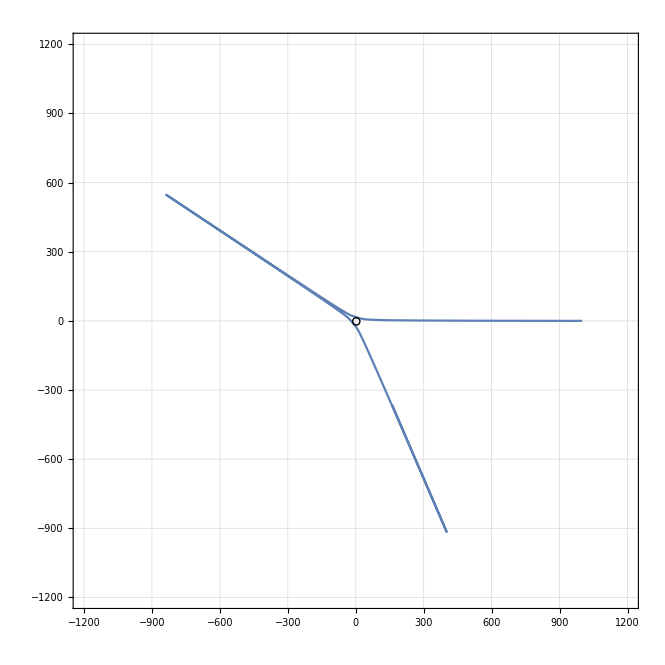

```mathematica
λmax=10^5;
sol=First@NDSolve[Join[eqs,ics,{WhenEvent[r[λ]≤16.,λmax=λ;"StopIntegration"]}],qHT,{λ,0,λmax}]
qScartHT[[1;;2]]/.sol;
Show[{ParametricPlot[%,{λ,0,λmax},PlotRange->1.2*10^3*{{-1,1},{-1,1}},Frame->True,Axes->False,GridLines->Automatic],Graphics[Circle[{0,0},16]]}]
```

## Kerr

```mathematica
qKerr={t[λ],r[λ],θ[λ],ϕ[λ]};
KerrRules={a->J/M,Σ->r^2+a^2 Cos[θ]^2,Δ->r^2-rs r+a^2,rs->2M}
qScartKerr={√(r^2+a^2)Sin[θ]Cos[ϕ],√(r^2+a^2)Sin[θ]Sin[ϕ],r Cos[θ]}//.KerrRules/.(#[[0]]->#&/@qKerr)
DiagonalMatrix[{-(1-(rs r)/Σ),Σ/Δ,Σ,(r^2+a^2+(rs r a^2)/Σ)Sin[θ]^2}];
SparseArray[{{1,4}->-(rs r a)/Σ Sin[θ]^2 ,{4,1}->-(rs r a)/Σ Sin[θ]^2 },{4,4}]//Normal;
gddKerrRaw=%+%%;
gddKerr=%//.KerrRules/.(#[[0]]->#&/@qKerr)
guuKerr=Inverse[gddKerr];

DgKerr=Dg[gddKerr,qKerr];
Γ2MKerr=genMΓ2All[genMΓ1All[DgKerr[[1]]],guuKerr];
Γ2Kerr=Γ[Γ2MKerr];
```

{a→J/M,Σ→r^2+a^2 Cos[θ]^2,Δ→a^2+r^2-r rs,rs→2 M}

{Cos[ϕ[λ]] √(J^2/M^2+r[λ]^2) Sin[θ[λ]],√(J^2/M^2+r[λ]^2) Sin[θ[λ]] Sin[ϕ[λ]],Cos[θ[λ]] r[λ]}

{{-1+(2 M r[λ])/((J^2 Cos[θ[λ]]^2)/M^2+r[λ]^2),0,0,-(2 J r[λ] Sin[θ[λ]]^2)/((J^2 Cos[θ[λ]]^2)/M^2+r[λ]^2)},{0,((J^2 Cos[θ[λ]]^2)/M^2+r[λ]^2)/(J^2/M^2-2 M r[λ]+r[λ]^2),0,0},{0,0,(J^2 Cos[θ[λ]]^2)/M^2+r[λ]^2,0},{-(2 J r[λ] Sin[θ[λ]]^2)/((J^2 Cos[θ[λ]]^2)/M^2+r[λ]^2),0,0,(J^2/M^2+r[λ]^2+(2 J^2 r[λ])/(M ((J^2 Cos[θ[λ]]^2)/M^2+r[λ]^2))) Sin[θ[λ]]^2}}

```mathematica
geodesicKerr=Array[0==D[qKerr[[#1]],{λ,2}]
+Sum[Γ2Kerr[#,i,j]D[qKerr[[j]],λ]*D[qKerr[[i]],λ],{i,1,4},{j,1,4}]&,4]//Expand//Simplify;
```

```mathematica
ClearAll[solveKerr];
solveKerr[pars_,ics_,λmax_,uu0_:-1.]:=Module[{λm,rmin,sol,solKart,eqs,dt0,uuDotud},
	λm=λmax;
	rmin=(M+√(-J^2/M^2+M^2))/.pars;
	dt0=Last@NSolve[uu0==D[qKerr,λ].gddKerr.D[qKerr,λ]/.pars/.λ->0/.(ics/.Equal->Rule),dtdτ0];
	Print[dt0];
	eqs=geodesicKerr/.pars;
	sol=First@NDSolve[Join[eqs,ics/.dt0,{WhenEvent[r[λ]≤1.2*rmin,λm=λ;"StopIntegration"]}],qKerr,{λ,0,λm},PrecisionGoal->10,AccuracyGoal->10];
	sol=sol/.InterpolatingFunction[x___][λ]:>If[λ<=λm,InterpolatingFunction[x][λ],InterpolatingFunction[x][λm]];
	solKart[x_/;NumericQ[x]]:=qScartKerr/.pars/.sol/.λ->x;
	uuDotud[x_/;NumericQ[x]]:=D[qKerr,λ].gddKerr.D[qKerr,λ]/.pars/.sol/.D[sol,λ]/.λ->x;
	Association@{"λm"->λm,"rmin"->rmin,"dt0"->dt0,"sol"->sol,"solKart"->solKart,"eqs"->eqs,"uuDotud"->uuDotud}
]
```

### Free falling on the x-Axis

```mathematica
ics=(#->0/.λ->0&/@Flatten[{qKerr,D[qKerr,λ]}])/.(Rule[#[[1]],0]->#&/@{r[0]->50.,r'[0]->0,θ[0]->π/2,ϕ'[0]->0,t'[0]->dtdτ0})/.Rule->Equal
```

{t[0]==0,r[0]==50.,θ[0]==π/2,ϕ[0]==0,t'[0]==dtdτ0,r'[0]==0,θ'[0]==0,ϕ'[0]==0}

```mathematica
sol1=solveKerr[{M->2*MSkm,J->1.*(MSkm)^2},ics,300];
sol4=solveKerr[{M->2*MSkm,J->4.*(MSkm)^2},ics,300];
```

{dtdτ0→1.06487}

{dtdτ0→1.06487}

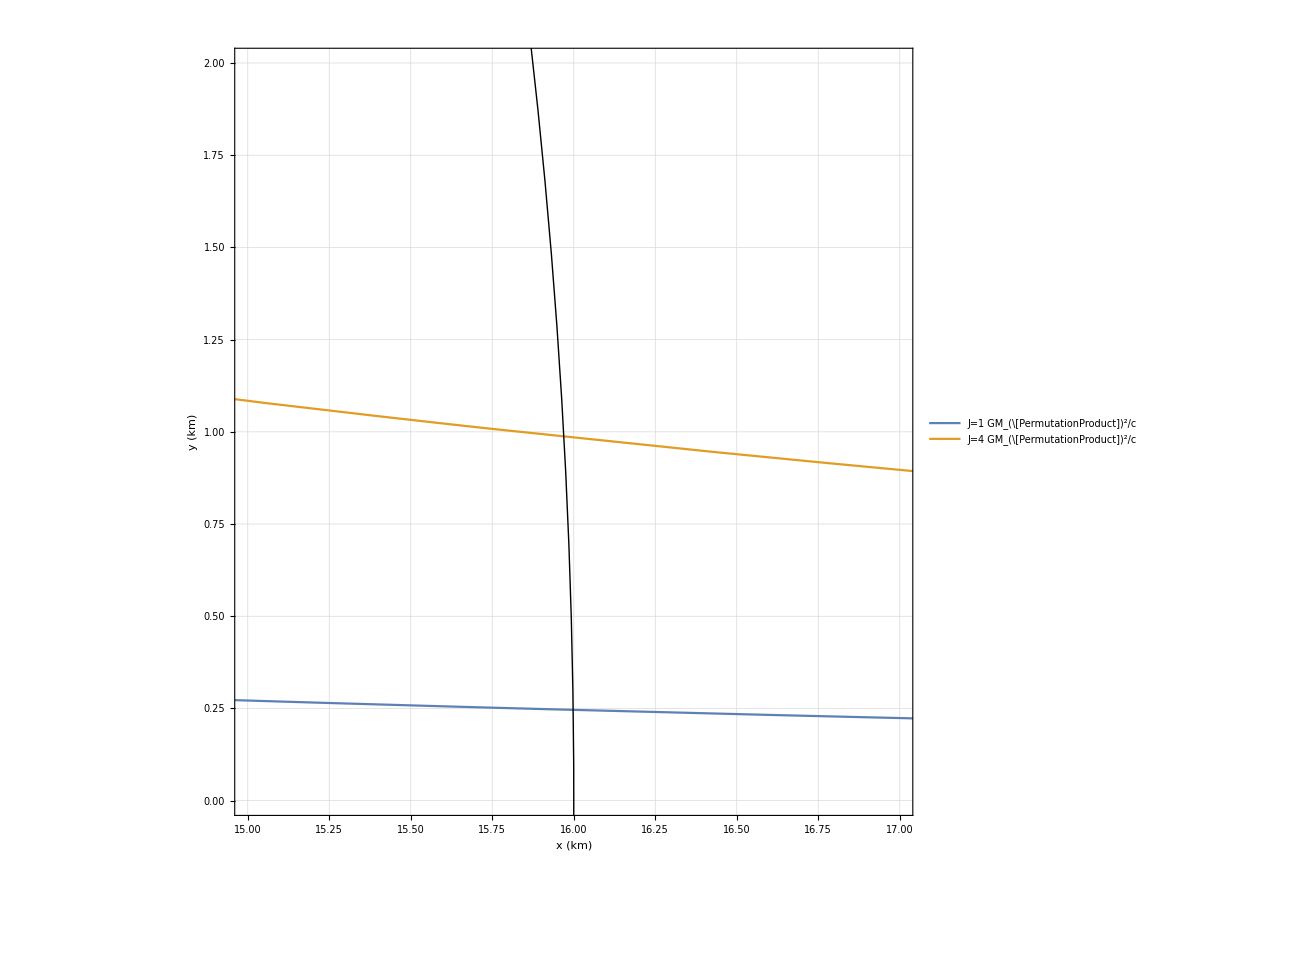

```mathematica
Show[{ParametricPlot[{sol1["solKart"][λ][[1;;2]],sol4["solKart"][λ][[1;;2]]},{λ,0,250},PlotRange->{{15,17},{0,2}},Frame->True,Axes->False,GridLines->Automatic,FrameLabel->{"x (km)","y (km)"},PlotLegends->Placed[{"J=1 GM_(\[PermutationProduct])^2/c","J=4 GM_(\[PermutationProduct])^2/c"},{Left,Top}]],
ParametricPlot[qScartKerr[[1;;2]]/.r[λ]->(M+√(-J^2/M^2+M^2))/.parsKerr/.θ[λ]->π/2,{ϕ[λ],0,2π},PlotStyle->Black],Graphics[{Black,Circle[{0,0},16]}]}]
```

{{6.51968 Cos[ϕ[λ]],6.51968 Sin[ϕ[λ]]},{4.17637 Cos[ϕ[λ]],4.17637 Sin[ϕ[λ]]}}

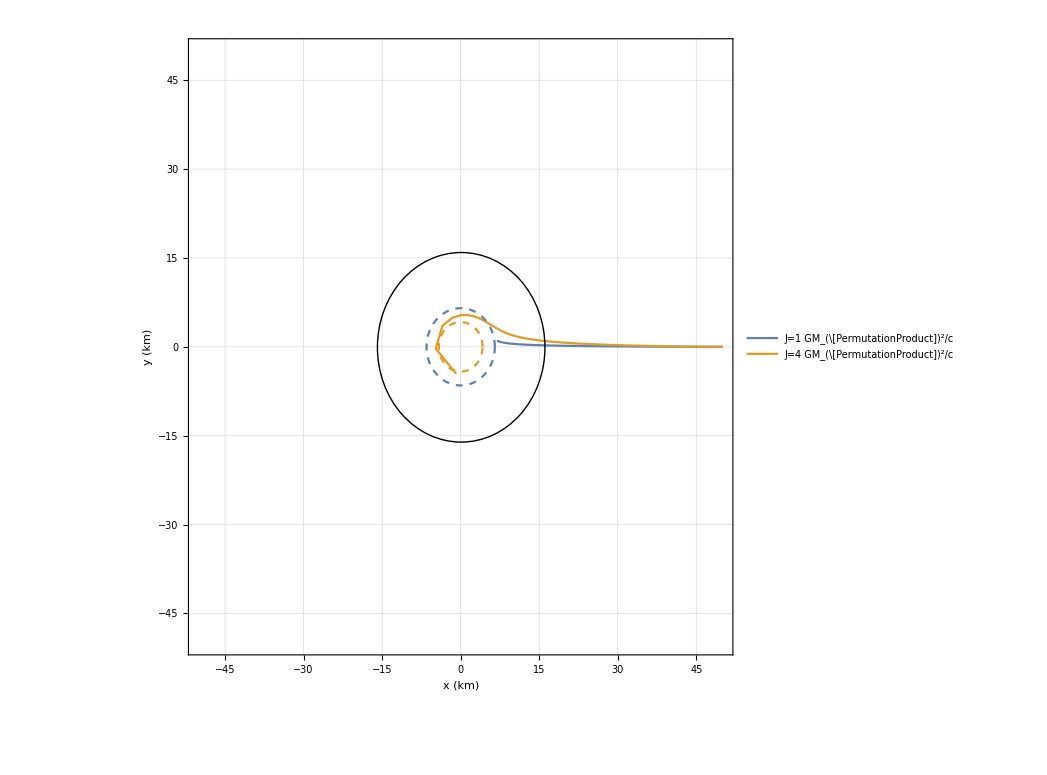

```mathematica
qScartKerr[[1;;2]]/.parsKerr/.θ[λ]->π/2/.r[λ]->#&/@{sol1["rmin"],sol4["rmin"]}
Show[{ParametricPlot[{sol1["solKart"][λ][[1;;2]],sol4["solKart"][λ][[1;;2]]},{λ,0,500},PlotRange->50*{{-1,1},{-1,1}},Frame->True,Axes->False,GridLines->Automatic,FrameLabel->{"x (km)","y (km)"},PlotLegends->Placed[{"J=1 GM_(\[PermutationProduct])^2/c","J=4 GM_(\[PermutationProduct])^2/c"},{Left,Top}]],
ParametricPlot[%,{ϕ[λ],0,2π},PlotStyle->Dashed],Graphics[{Black,Circle[{0,0},16]}]}]
```

### Orbits

```mathematica
ics=(#->0/.λ->0&/@Flatten[{qKerr,D[qKerr,λ]}])/.(Rule[#[[1]],0]->#&/@{r[0]->10^3,θ[0]->π/2.,ϕ[0]->π/4.,ϕ'[0]->12*10^-6,t'[0]->dtdτ0})/.Rule->Equal
t1=1.0*10^6;
solAsmpt=solveKerr[{M->2*MSkm,J->0*1.0*(MSkm)^2},ics,t1];
```

{t[0]==0,r[0]==1000,θ[0]==1.5708,ϕ[0]==0.785398,t'[0]==dtdτ0,r'[0]==0,θ'[0]==0,ϕ'[0]==3/250000}

{dtdτ0→1.00304}

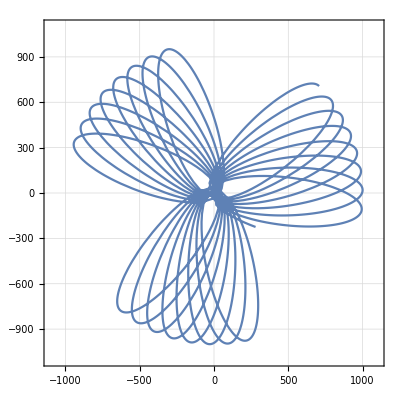

```mathematica
Show[{ParametricPlot[{solAsmpt["solKart"][λ][[1;;2]]},{λ,0,t1},PlotRange->1.1*10^3*{{-1,1},{-1,1}},Frame->True,Axes->False,GridLines->Automatic]}]
```